# Développement d'une fonction

## Exemple

```mathematica
Subscript[f, 1][x_]:=1/(√2)
```

```mathematica
Subscript[f, 2][x_]:=√(3/2) x
```

```mathematica
Subscript[f, 3][x_]:=1/2 √(5/2) (3 x^2-1)
```

```mathematica
Subscript[f, 4][x_]:=1/2 √(7/2) x (-3+5 x^2)
```

```mathematica
Subscript[f, 5][x_]:=(3 (3-30 x^2+35 x^4))/(8 √2)
```

```mathematica
Subscript[f, 6][x_]:=1/8 √(11/2) x (15-70 x^2+63 x^4)
```

```mathematica
Subscript[f, 7][x_]:=1/16 √(13/2) (-5+105 x^2-315 x^4+231 x^6)
```

```mathematica
Subscript[f, 8][x_]:=1/16 √(15/2) x (-35+315 x^2-693 x^4+429 x^6)
```

```mathematica
Subscript[f, 9][x_]:=1/128 √(17/2) (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8)
```

```mathematica
Subscript[f, 10][x_]:=1/128 √(19/2) x (315-4620 x^2+18018 x^4-25740 x^6+12155 x^8)
```

```mathematica
w[x_]:=1
```

### Intervalle d'orthogonalité

```mathematica
a:=-1
```

```mathematica
b:=1
```

### Orthonormalité

```mathematica
Table[∫_a^b w[x]Subscript[f, i][x]* Subscript[f, j][x]ⅆx,{i,1,10},{j,1,10}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Table[KroneckerDelta[i,j],{i,1,10},{j,1,10}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Développement de F(x)

### La fonction à développer

```mathematica
F[x_] :=Abs[ x]
```

### Les coéfficients

```mathematica
Subscript[c, n_]:=∫_a^b w[x]Subscript[f, n][x]*F[x]ⅆx
```

```mathematica
Table[Subscript[c, n],{n,1,10}]
```

{1/(√2),0,(√(5/2))/4,0,-1/(8 √2),0,(√(13/2))/64,0,-(√(17/2))/128,0}

### Développement

```mathematica
Fdev[x_]=∑_(n=1)^10 Subscript[c, n] Subscript[f, n][x]
```

1/2+5/16 (-1+3 x^2)-3/128 (3-30 x^2+35 x^4)+(13 (-5+105 x^2-315 x^4+231 x^6))/2048-(17 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8))/32768

## Représentation

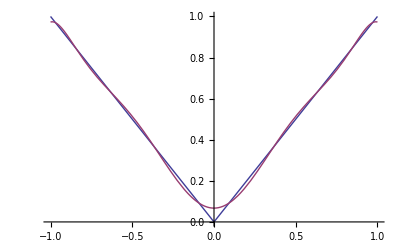

```mathematica
Plot[Evaluate[{F[x],Fdev[x]}],{x,-1,1},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[{F[x],∑_(n=1)^N Subscript[c, n] Subscript[f, n][x]}],{x,-1,1},PlotRange->All],{N,1,10,1},ControlType->Setter]
```